Coordinates and Graphics

We’ve used ListPlot and ListLinePlot to plot lists of values, where each value appears after the one before. But by giving lists containing pairs of coordinates instead of single values, we can use these functions to plot points at arbitrary positions.

Plot a list of values where each value appears after the one before:

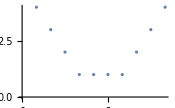

```mathematica
ListPlot[{4,3,2,1,1,1,1,2,3,4}]
```

Plot a sequence of arbitrary points specified by {x, y} coordinates:

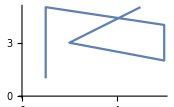

```mathematica
ListLinePlot[{{1,1},{1,5},{6,4},{6,2},{2,3},{5,5}}]
```

The position of each point here is specified by {x, y} coordinates. Following the standard convention in mathematics, the x value says how far across horizontally the point should be; the y value says how far up vertically it should be.

Generate a sequence of random {x, y} coordinates:

```mathematica
Table[RandomInteger[20],10,2]
```

{{19,8},{11,20},{14,15},{5,8},{6,4},{16,14},{1,17},{10,7},{5,6},{17,2}}

Another way to get random coordinates:

```mathematica
RandomInteger[20,{10,2}]
```

{{2,2},{20,18},{16,2},{13,13},{6,15},{11,18},{10,20},{17,20},{8,14},{2,10}}

Plot 100 points at random coordinates:

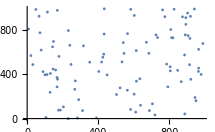

```mathematica
ListPlot[Table[RandomInteger[1000],100,2]]
```

We can use coordinates to construct graphics. Earlier we saw how to make graphics of one circle. To make graphics of more than one circle we have to say where each circle is, which we can do by giving the coordinates of their centers.

Place circles by giving the coordinates of their centers:

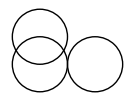

```mathematica
Graphics[{Circle[{1,1}],Circle[{1,2}],Circle[{3,1}]}]
```

If we apply color styles it’s easier to see which circle is which:

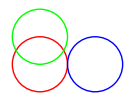

```mathematica
Graphics[{Style[Circle[{1,1}],Red],Style[Circle[{1,2}],Green],Style[Circle[{3,1}],Blue]}]
```

Make a graphic with 100 randomly placed circles, each with center coordinates up to 50:

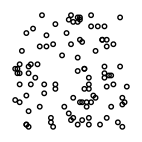

```mathematica
Graphics[Table[Circle[RandomInteger[50,2]],100]]
```

A 2D array of circles, arranged so that they just touch:

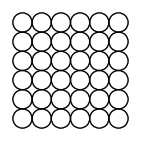

```mathematica
Graphics[Table[Circle[{x,y}],{x,0,10,2},{y,0,10,2}]]
```

Circle[{x,y}] means a circle centered at position {x,y}. If you don’t say otherwise, the circle is given radius 1. You can make a circle of any radius using Circle[{x,y},r].

Use different radii for different circles:

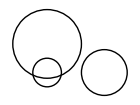

```mathematica
Graphics[{Circle[{1,1},0.5],Circle[{1,2},1.2],Circle[{3,1},0.8]}]
```

Make 10 concentric circles:

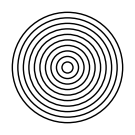

```mathematica
Graphics[Table[Circle[{0,0},r],{r,10}]]
```

Draw larger circles with centers that shift progressively to the right:

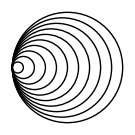

```mathematica
Graphics[Table[Circle[{x,0},x],{x,10}]]
```

Pick both positions and radii at random:

```mathematica
Graphics[Table[Circle[RandomInteger[50,2],RandomInteger[10]],100]]
```

-Graphics-

RegularPolygon works much the same as Circle and Disk, except that in addition to giving the position of the center and the size, you also have to specify how many sides the polygon should have.

Make graphics of a size-1 regular pentagon and a size-0.5 regular heptagon:

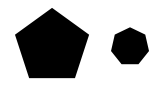

```mathematica
Graphics[{RegularPolygon[{1,1},1,5],RegularPolygon[{3,1},0.5,7]}]
```

You can mix different kinds of graphics objects:

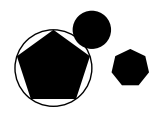

```mathematica
Graphics[{RegularPolygon[{1,1},1,5],Circle[{1,1},1],RegularPolygon[{3,1},.5,7],Disk[{2,2},.5]}]
```

To make arbitrary graphics, you need the basic graphics primitives Point, Line and Polygon. Point[{x,y}] represents a point at coordinate position {x,y}. To get multiple points, you can either give a list of Point[{x,y}]s, or you can give a list of coordinate positions inside a single Point.

Graphics of three points at specified positions:

```mathematica
Graphics[{Point[{0,0}],Point[{2,0}],Point[{1,1.5}]}]
```

-Graphics-

An alternative form, where all the coordinate positions are collected in a single list:

```mathematica
Graphics[Point[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

Make a line joining the positions:

```mathematica
Graphics[Line[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

Make a polygon with corners at the positions you give:

```mathematica
Graphics[Polygon[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

RegularPolygon makes a regular polygon in which all sides and angles are the same. Polygon lets you make any polygon, even strange ones that fold over themselves.

A polygon with 20 corners at random coordinates below 100; the polygon folds over itself:

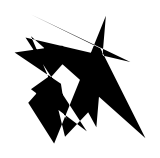

```mathematica
Graphics[Polygon[Table[RandomInteger[100],20,2]]]
```

The things we’ve done so far here immediately generalize to 3D. Instead of having two coordinates {x, y} we have three: {x, y, z}. In the Wolfram Language, x by default goes across the screen, y goes “into” the screen, and z goes up the screen.

Two spheres stacked on top of each other:

```mathematica
Graphics3D[{Sphere[{0,0,0}],Sphere[{0,0,2}]}]
```

-Graphics3D-

A 3D array of spheres (radius 1/2 makes them just touch):

```mathematica
Graphics3D[Table[Sphere[{x,y,z},1/2],{x,5},{y,5},{z,5}]]
```

-Graphics3D-

A 3D array of points:

```mathematica
Graphics3D[Table[Point[{x,y,z}],{x,10},{y,10},{z,10}]]
```

-Graphics3D-

50 spheres at random 3D positions, with each coordinate running up to 10:

```mathematica
Graphics3D[Table[Sphere[RandomInteger[10,3]],50]]
```

-Graphics3D-

If you don’t say otherwise, 3D objects like spheres are drawn solid, so you can’t see through them. But just like you can specify what color something is, you can also specify its opacity. Opacity 1 means completely opaque, so you can’t see through it at all; opacity 0 means completely transparent.

Specify opacity 0.5 for all spheres:

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],Opacity[0.5]],50]]
```

-Graphics3D-

You can use Manipulate to make graphics—in 2D or 3D—that can be manipulated.

Manipulate the position and opacity of the dodecahedron:

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0}],Style[Dodecahedron[{x,0,0}],Opacity[o]]}],{x,1,3},{o,0.5,1}]
```

Vocabulary

Point[{x,y}] |   | a point at coordinates {x,y}
Line[{{1,1},{2,4},{1,2}}] |   | a line connecting specified coordinates 
Circle[{x,y}] |   | a circle with center at {x,y}
Circle[{x,y},r] |   | a circle with center at {x,y} and radius r 
RegularPolygon[{x,y},s,n] |   | a regular polygon with center {x,y}, size s and n sides
Polygon[{{1,1},{2,4},{1,2}}] |   | a polygon with the specified corners 
Sphere[{x,y,z}] |   | a sphere with center at {x,y,z}
Sphere[{x,y,z},r] |   | a sphere with center at {x,y,z} and radius r
Tetrahedron[{x,y,z}, s], ... |   | polyhedra with centers at {x,y,z} and side length s
Opacity[level] |   | specify an opacity level (0: transparent; 1: solid)

"11 Exercises Available"
"with 6 extras" | "Get Started »"

Make graphics of 5 concentric circles centered at {0,0} with radii 1, 2, ... , 5. »

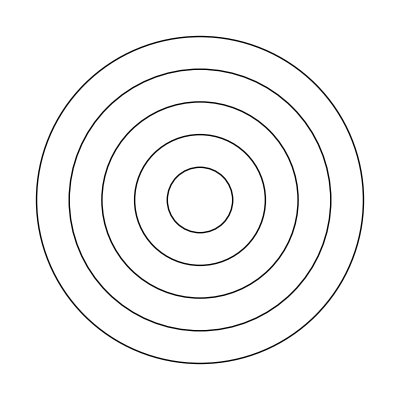
| Expected output: |  
  | -Graphics- |

Make 10 concentric circles with random colors. »

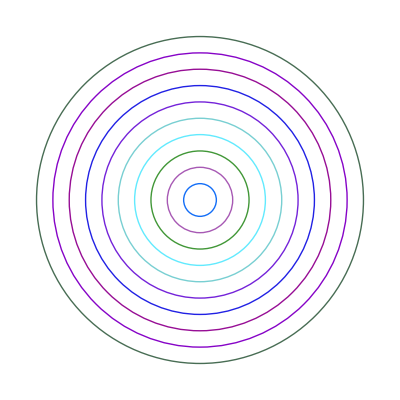
| Sample expected output: |  
  | -Graphics- |

Make graphics of a 10×10 grid of circles with radius 1 centered at integer points {x,y}. »

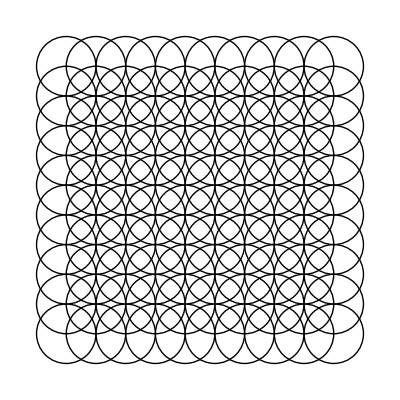
| Expected output: |  
  | -Graphics- |

Make a 10×10 grid of points with coordinates at integer positions up to 10. »

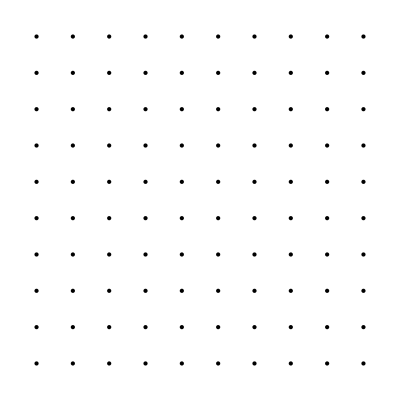
| Expected output: |  
  | -Graphics- |

Make a Manipulate with between 1 and 20 concentric circles. »

| Expected output: |  
  |  |

Place 50 spheres with random colors at random integer coordinates up to 10. »

| Sample expected output: |  
  | -Graphics3D- |

Make an 11×11×11 array of spheres with RGB components ranging from 0 to 1. The spheres should be centered at integer coordinates, and should just touch each other. »

| Expected output: |  
  | -Graphics3D- |

Make a Manipulate with t varying between −2 and +2 that contains circles of radius x centered at {t*x,0} with x going from 1 to 10. »

| Expected output: |  
  |  |

Make a 5×5 array of regular hexagons with size 1/2, centered at integer points. »

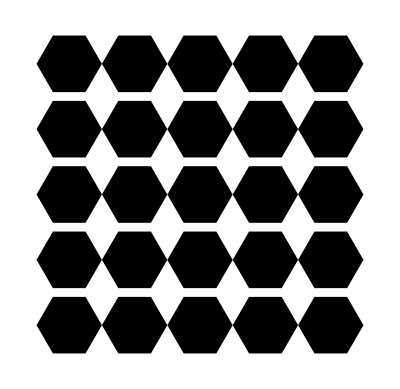
| Expected output: |  
  | -Graphics- |

Make a line in 3D that goes through 50 random points with integer coordinates randomly chosen up to 50. »

| Sample expected output: |  
  | -Graphics3D- |

Make a Manipulate of an icosahedron with side length varying from 1 to 2 and a dodecahedron with side length 1, both having opacity 0.5 and the same center. »

| Expected output: |  
  |  |

Make a Manipulate to create an n×n regular grid of points at integer positions, with n going from 5 to 20. »

| Expected output: |  
  |  |

Place 30 radius-1 circles with random colors at random integer coordinates up to 10. »

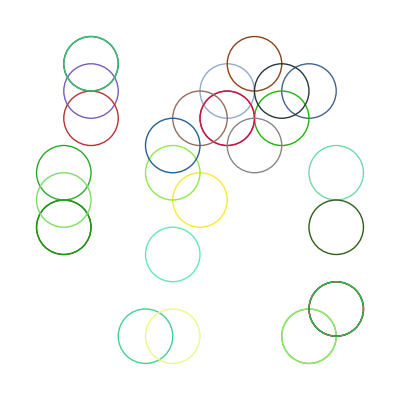
| Expected output: |  
  | -Graphics- |

Display 100 polygons with size 10, opacity .5, and random choices of colors, sides between 3 and 8, and integer coordinates up to 100. »

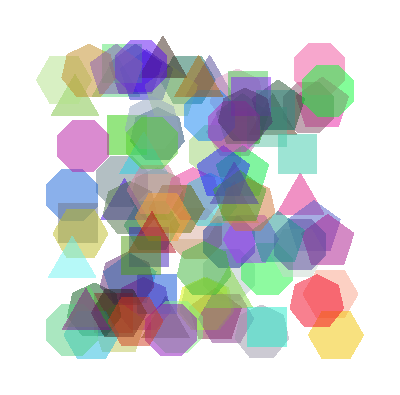
| Expected output: |  
  | -Graphics- |

Make a 10×10×10 array of points in 3D, with each point having a random color. »

| Expected output: |  
  | -Graphics3D- |

Take the first two digits of numbers from 10 to 100 and draw a line that uses them as coordinates. »

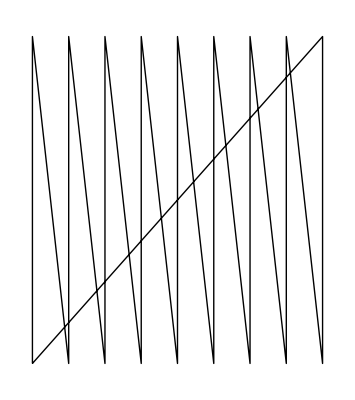
| Expected output: |  
  | -Graphics- |

Take the first 3 digits of numbers from 100 to 1000 and draw a line in 3D that uses them as coordinates. »

| Expected output: |  
  | -Graphics3D- |

Q&A

What determines the range of coordinates shown?

By default it’s picked automatically, but you can set it explicitly using the PlotRange option, as discussed in Section 20.

How can I put axes on graphics?

Use the option (see Section 20) Axes→True.

What is meant by the “size” of a regular polygon?

You can think of the corners of a regular polygon as being arranged on a circle centered at the center of the polygon. The “size” s in RegularPolygon[{x,y}, s, n] gives the radius of the circle.

How do I change the appearance of the edges of a polygon or disk?

Use EdgeForm inside Style.

What other graphics constructs are there?

Quite a few. Examples include Text (for placing text inside graphics), Arrow (for putting arrowheads on lines, etc.), Inset (for putting graphics inside graphics) and FilledCurve.

How do I get rid of the box around 3D graphics?

Use the option (see Section 20) Boxed→False.

Can I manually draw graphics in the Wolfram Language?

Yes. Use the function Canvas to create a canvas that is either blank or already has content. The result of your drawing will be graphics primitives that you can then manipulate further.

Tech Notes

The random circles here are drawn at integer coordinates. You can use RandomReal to place them at arbitrary coordinates.

Instead of using Style, you can give directives for graphics in a list, like {Red,Disk[ ]}. A particular directive will affect every graphics object that appears after it in the list.

In 2D graphics, objects are drawn in whatever order you give them, so later ones can cover up earlier ones.

You can apply geometric transformations to graphics objects using functions like Translate, Scale and Rotate.

Polygons that fold over themselves (say, to make a bowtie shape) are displayed using an even-odd rule.

3D graphics can include Cube, Tetrahedron, Dodecahedron, etc. and polyhedra specified by PolyhedronData, as well as shapes defined by arbitrary meshes of points in 3D space.

A convenient way to add to a list of coordinates is to use Threaded. {{1, 2}, {3, 4}, {5, 6}} + Threaded[{a, b}] gives {{1 + a, 2 + b}, {3 + a, 4 + b}, {5 + a, 6 + b}}.

More to Explore

Guide to Graphics in the Wolfram Language »